```mathematica
Odat:=Import["C:/Users/Shmuma/Work/RadioBoat/Sim/Stage1/O.dat"]
Adat:=Import["C:/Users/Shmuma/Work/RadioBoat/Sim/Stage1/A.dat"]
```

```mathematica
ListPlot[{Odat,Adat}]
```

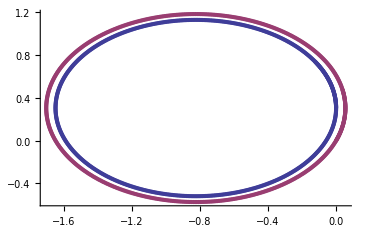

```mathematica
xo[t_]:=R*Cot[alpha]*(Cos[phi[t]]-1)
```

```mathematica
yo[t_]:=-R*Cot[alpha]*Sin[phi[t]]+R
```

```mathematica
phi[t_]:=-vel*Sin[alpha]*t/R
```

```mathematica
xa[t_]:=R*Sin[-phi[t]]+xo[t]
```

```mathematica
ya[t_]:=-R*Cos[-phi[t]]+yo[t]
```

```mathematica
R:=0.3
```

```mathematica
alpha:=20*Degree
```

```mathematica
vel:=0.1
```

```mathematica
ya[0]
```

0.

```mathematica
yo[0]
```

0.3

```mathematica
yo[0.1]
```

0.309397

```mathematica
yo[0.2]
```

0.318792

```mathematica
R*Cot[alpha]
```

0.824243

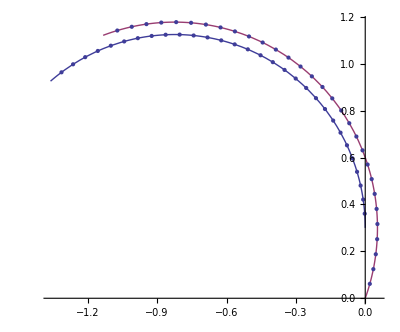

```mathematica
ParametricPlot[{{xo[t],yo[t]},{xa[t],ya[t]}},{t,0,20},Mesh->30]
```